## Bayesian Inference

### Prior, likelihood and posterior

```mathematica
p[x_]:=1/Sqrt[2Pi] Exp[-x^2/2];
pd[x_]:=1/0.5/Sqrt[2Pi] Exp[-(x-2)^2/2/0.5^2];

denom=NIntegrate[p[x] pd[x],{x,-Infinity,Infinity}];
ppost[x_]:=p[x] pd[x]/denom
```

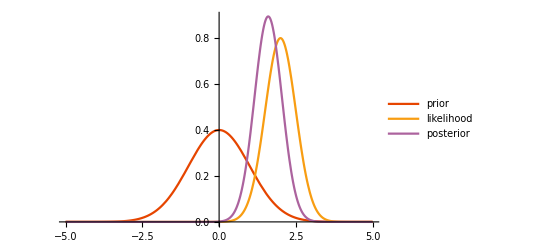

```mathematica
Plot[{p[x],pd[x],ppost[x]},{x,-5,5},PlotRange->Full,PlotLegends->{"prior","likelihood","posterior"},PlotStyle->ColorData[113]]
```

### Acceptance-rejection sampling

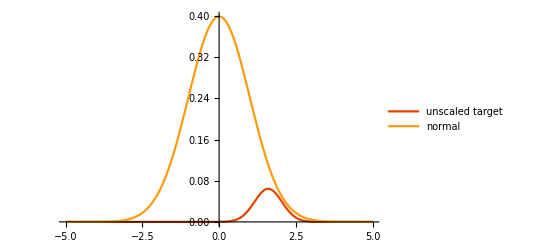

```mathematica
punscaled[x_]:=pd[x] p[x];
Plot[{punscaled[x],p[x]},{x,-5,5},PlotRange->Full,PlotLegends->{"unscaled target","normal","posterior"},PlotStyle->ColorData[113]]
```

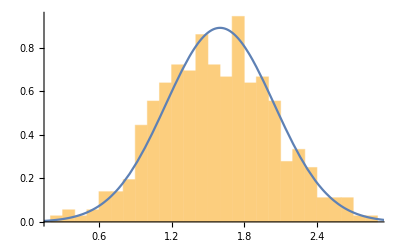

```mathematica
list={};
For[i=1,i<5000,i++,
x=RandomVariate[NormalDistribution[]];
w= pd[x]p[x]/p[x];
u=RandomVariate[UniformDistribution[{0,1}]];
If[u<w,AppendTo[list,x]]
]
hist=Histogram[list,{0.1},"PDF"];
plot=Plot[ppost[x],{x,0,3}];
Show[hist,plot]
```

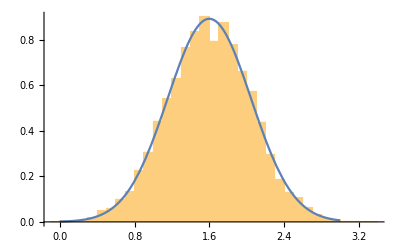

```mathematica
list={};
For[i=1,i<100000,i++,
x=RandomVariate[NormalDistribution[]];
w= pd[x]p[x]/p[x];
u=RandomVariate[UniformDistribution[{0,1}]];
If[u<w,AppendTo[list,x]]
]
hist=Histogram[list,{0.1},"PDF"];
plot=Plot[ppost[x],{x,0,3}];
Show[hist,plot]
```